# Ukázka využití Schlömilchovy věty na přerovnání řady

Simona Buryšková, Jan Hrubeš

## Section Zkoumaná řada

Vypíšeme si pro představu několik prvních členů zkoumané řady:

```mathematica
clenyUkazka = Table[(-1)^(k-1)/k, {k,1,10}]
cleny = Table[(-1)^(k-1)/k, {k,1,100}];
```

{1,-1/2,1/3,-1/4,1/5,-1/6,1/7,-1/8,1/9,-1/10}

Posloupnost částečných součtů pro prvních 100 členů vypadá takto (zkráceně):

```mathematica
castecnesoucty = Accumulate[cleny];
Short[castecnesoucty,3]
```

{1,1/2,5/6,7/12,«93»,9594516020402274303348963549166209678997/13944075045942495432906761787062460711360,9735365263290582338024789425803204231637/13944075045942495432906761787062460711360,47979622564155786918478609039662898122617/69720375229712477164533808935312303556800}

Řada je neabsolutně konvergentní1 (harmonická řada totiž diverguje) a platí .

Konvergenci posloupnosti částečných součtů k součtu řady znázorňuje Graf 1.

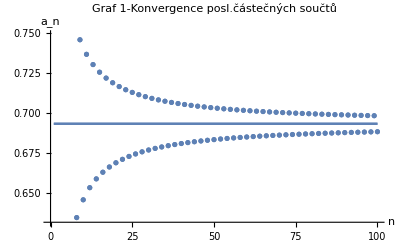

```mathematica
castecnesouctyPlot = ListPlot[castecnesoucty];
limitaPuvodni= Plot[Log[2], {x, 1, 100}];
Show[castecnesouctyPlot, limitaPuvodni,%21,AxesLabel->{HoldForm[n],HoldForm[a_n]},PlotLabel->HoldForm[Graf 1 - Konvergence posl.částečných součtů],LabelStyle->{GrayLevel[0]}]
```

## Section Přerovnání řady pomocí Schlömilchova algoritmu

## Section Závěr

Shrnutí, odkazy na grafy a vzorce.

## Section Zdroje

1	KOPÁČEK, Jiří. Matematická analýza nejen pro fyziky (II). 4. vyd. Praha: Matfyzpress, 2015. ISBN 978-80-7378-282-5.